```mathematica
http://reference.wolfram.com/language/ref/BetaBinomialDistribution.html
```

```mathematica
PolyaDistribution[p_,α_,n_]:=BetaBinomialDistribution[p/α,(1-p)/α,n]
```

```mathematica
PDF[PolyaDistribution[p,α,n],k]
```

Piecewise[{{(Binomial[n,k] Pochhammer[(1-p)/α,-k+n] Pochhammer[p/α,k])/Pochhammer[(1-p)/α+p/α,n], 0≤k≤n}, {0, True}}]

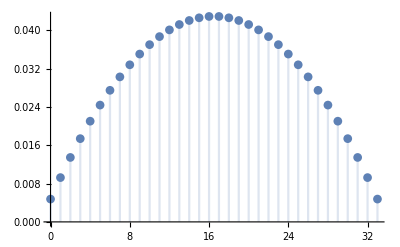

```mathematica
DiscretePlot[PDF[BetaBinomialDistribution[2,2,33],x]//Evaluate,{x,0,33},PlotMarkers->Automatic]
```

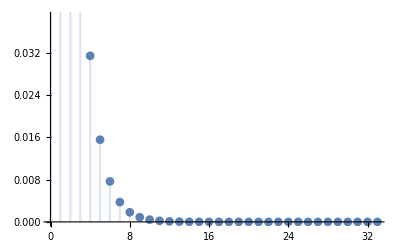

```mathematica
DiscretePlot[PDF[BetaBinomialDistribution[1,99,100],x]//Evaluate,{x,0,33},PlotMarkers->Automatic]
```